## Formulas

```mathematica
Clear[plotRay,plotPoint,plot]
plotRay[a_,u_]:=Arrow[{a,a+u}]
plotPoint[a_]:=Disk[a,0.2]
plot[vp_,lp_,vpn_,f_]:=With[{r=0.07},Graphics[{
Blue,Disk[vp,0.2],
Red,Disk[lp,0.2],
Table[{
GrayLevel[f[vp,lp,pn⟦1⟧,pn⟦2⟧]],
Disk[pn⟦1⟧,r],
Black,Circle[pn⟦1⟧,r],
Black,plotRay[pn⟦1⟧+r pn⟦2⟧,pn⟦2⟧]
},{pn,vpn}]
},Frame->True]]
```

```mathematica
Clear[shade,shadeLambert]
shadeLambert[vp_,lp_,p_,n_]:=Module[{l,v,h},
l=Normalize[lp-p];
v=Normalize[vp-p];
h=Normalize[l+v];
Max[0,n.l]/(1+0.005 Norm[lp-p]^2)
]
shadeUnreal[vp_,lp_,p_,n_]:=Module[{l,v,h,dvn,dvh,dln,dnh,L,α,z,D,rough,k,G,F0,F},
l=1.Normalize[lp-p];
v=1.Normalize[vp-p];
h=1.Normalize[l+v];
dvn=Dot[v,n];
dvh=Dot[v,h];
dln=Dot[l,n];
dnh=Dot[n,h];
L=10 Max[0,dln]/(1+0.005 Norm[lp-p]^2);
rough=0.3;
z=4dln dvn;
α=rough^2;
(* Normal Distribution Function *)
D=α^2/(π(dnh^2(α^2-1)+1)^2);
(* Geometric Shadowing *)
k=α/2;(*(rough+1)^2/8;*)
G=dln/(dln(1-k)+k)dvn/(dvn(1-k)+k);
(* Fresnel *)
F0=0.5;
F=F0+(1-F0)2^((-5.55473dvh-6.98316)dvh);
(*Print[D];Print[G];Print[F];Print[z];Print[L];*)
(D G F)/z L
]
shade=shadeUnreal;
```

## Approximations

```mathematica
Plot[{(1-dvh)^5,2^((-5.55473dvh-6.98316)dvh)},{dvh,0,1}]
```

```mathematica
Plot[{x^2/2,(x+1)^2/8,x^2 √(2/π)},{x,0,1}]
```

```mathematica
Plot3D[1/(π α^2)dnh^(2/α^2-2),{α,0,1},{dnh,0,1},AxesLabel->{a,dnh}]
Plot3D[α^2/(π(dnh^2(α^2-1)+1)^2),{α,0,1},{dnh,0,1},AxesLabel->{a,dnh}]
```

## Results

```mathematica
shade[vp,lp,{3,-2},{0,1}]
```

0.275074

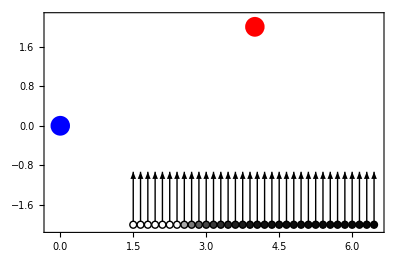

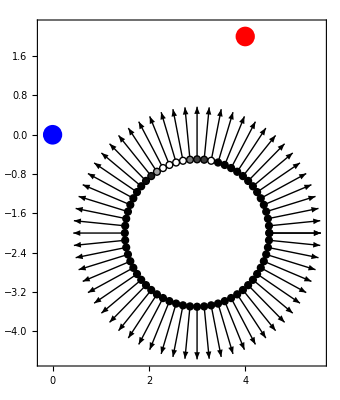

```mathematica
vp={0,0};
lp={4,2};
plot[vp,lp,Table[{{x,-2},{0,1}},{x,1.5,6.5,.15}],shade]
plot[vp,lp,Table[With[{n={Cos@α,Sin@α}},{{3,-2}+1.5n,n}],{α,0,2π,(2π)/64}],shade]
```